```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adityak/Aditya/git/root_tracking/Mathematica/SRSPM

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

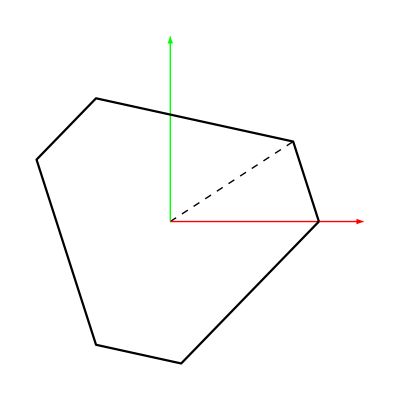

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

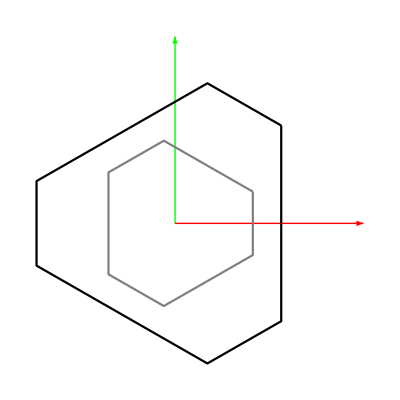

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initposeC = Join[qx/.roots[[1]],iksolC[qx/.rootsC[[1]]]][[;;-7]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Plotting the SRSPM:

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
```

```mathematica
qfull = Join[qx, qvar];
```

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
index = 2;
initpose = Join[qx/.roots[[index]], iksolC[qx/.roots[[index]]]];
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

```mathematica
(*To plot only the top platform*)
```

```mathematica
(*plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.8],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-direction[[i]]*la/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, axis]
]*)
```

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]};
(*parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0};*)
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, 2π, 2π/50}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

## Path generation

## Newton-Raphson method for root tracking

### Real roots:

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
Inner[List, q/.qrule, Table[_Complex, {i, Length[q]}], List]
```

{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Norm[nvec]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
initpose[[7;;]]
```

{0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
testconfig = initpose[[7;;-7]];
```

```mathematica
tic[]
tempϕ = testconfig;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηconfig, cJηconfig];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.04552 seconds.

CPU time consumed: 0.045502 seconds.

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Inner[List, Join[qx, q/.qrule], Table[_Complex, {i, Length[Join[qx, q]]}], List]
```

{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
p
```

{p1,p2,p3,p4,p5,p6}

```mathematica
s
```

{s1,s2,s3,s4,s5,s6}

```mathematica
ηext//N
```

{0.732576-(0.220568 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)-(0.536747 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l1 Cos[ψ1] Sin[ϕ1],0.680685-(1.07349 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.220568 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l1 Sin[ψ1],-(1.07349 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(0.441137 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l1 Cos[ϕ1] Cos[ψ1],0.223203-(0.575121 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.0773559 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l2 Cos[ψ2] Sin[ϕ2],0.974772+(0.154712 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.575121 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l2 Sin[ψ2],(0.154712 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(1.15024 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l2 Cos[ϕ2] Cos[ψ2],-0.955779-(0.354553 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.459391 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l3 Cos[ψ3] Sin[ϕ3],0.294087+(0.918783 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)-(0.354553 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l3 Sin[ψ3],(0.918783 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)-(0.709105 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l3 Cos[ϕ3] Cos[ψ3],-0.955779+(0.354553 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.459391 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l4 Cos[ψ4] Sin[ϕ4],-0.294087+(0.918783 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.354553 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l4 Sin[ψ4],(0.918783 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(0.709105 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l4 Cos[ϕ4] Cos[ψ4],0.223203+(0.575121 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)+(0.0773559 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l5 Cos[ψ5] Sin[ϕ5],-0.974772+(0.154712 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.575121 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l5 Sin[ψ5],(0.154712 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(1.15024 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l5 Cos[ϕ5] Cos[ψ5],0.732576+(0.220568 (2. c1 c2-2. c3))/(1.+c1^2+c2^2+c3^2)-(0.536747 (1.+c1^2-1. c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. x+l6 Cos[ψ6] Sin[ϕ6],-0.680685-(1.07349 (c1 c2+c3))/(1.+c1^2+c2^2+c3^2)+(0.220568 (1.-1. c1^2+c2^2-1. c3^2))/(1.+c1^2+c2^2+c3^2)-1. y-1. l6 Sin[ψ6],-(1.07349 (-1. c2+c1 c3))/(1.+c1^2+c2^2+c3^2)+(0.441137 (c1+c2 c3))/(1.+c1^2+c2^2+c3^2)-1. z+l6 Cos[ϕ6] Cos[ψ6]}

```mathematica
initpose
cηext@@initpose
```

{0.2,0,1.28,0.2,0,0,0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

{-7.80626×10^-18-1.15633×10^-16 ⅈ,0.+4.902×10^-18 ⅈ,-2.22045×10^-16+2.06692×10^-18 ⅈ,2.77556×10^-17-1.39993×10^-16 ⅈ,-5.55112×10^-17+2.9267×10^-16 ⅈ,2.22045×10^-16+7.71624×10^-17 ⅈ,-1.11022×10^-16-2.68985×10^-16 ⅈ,3.46945×10^-17+2.14124×10^-16 ⅈ,-2.22045×10^-16+1.27234×10^-16 ⅈ,1.11022×10^-16-8.38346×10^-17 ⅈ,1.17961×10^-16+2.33547×10^-16 ⅈ,0.+5.78274×10^-17 ⅈ,-1.38778×10^-17-9.9097×10^-17 ⅈ,-2.22045×10^-16+3.71585×10^-17 ⅈ,-2.22045×10^-16-2.499×10^-17 ⅈ,1.75207×10^-16-9.51422×10^-17 ⅈ,-2.77556×10^-16+1.56756×10^-16 ⅈ,2.22045×10^-16-6.22413×10^-17 ⅈ}

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initpose[[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.02281 seconds.

CPU time consumed: 0.022824 seconds.

```mathematica
xlist = ϕlist[[;;, ;;3]];
```

```mathematica
xlist[[1]]
```

{0.2,0,1.28}

```mathematica
Graphics3D[Sphere[{Chop[xlist[[1;;]]]}, 0.01]]
```

-Graphics3D-

```mathematica
initposes = Table[Join[qx/.roots[[i]], iksolC[qx/.roots[[i]]]], {i, Length[roots]}];
```

```mathematica
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ, cηext, cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.02247 seconds.

CPU time consumed: 0.022469 seconds.

```mathematica
xlist = ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksolC[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

```mathematica
(*Tracking all the sets of roots together*)
```

```mathematica
testext = initposes[[;;, ;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = Table[NRTracking[legvals[[i]], tempϕ[[j]], cηext, cJηext],{j, Length[tempϕ]}];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.20969 seconds.

CPU time consumed: 0.209857 seconds.

```mathematica
ϕlist//Dimensions
```

{51,8,18}

```mathematica
ϕlist[[1]]//Dimensions
```

{8,18}

```mathematica
initpose
```

{0.2,0,1.28,0.2,0,0,0.00305624-8.47269×10^-17 ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,-0.0946901-9.49786×10^-17 ⅈ,0.00349011-7.94231×10^-17 ⅈ,0.336276-3.59163×10^-18 ⅈ,0.286891-1.94522×10^-16 ⅈ,-0.0210274-1.35667×10^-16 ⅈ,0.0247844-1.74422×10^-16 ⅈ,-0.395383-3.49377×10^-17 ⅈ,-0.379795-1.31157×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
tempU = 51;
Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[tempU]], iksolC[xlist[[tempU]]]], List]],ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-1.436630585725502,-2.436545269611847,1.857239809311155},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.029245185453707287,-0.04235819972678877,0.9986743723775453}]
```

-Graphics3D-

### Complex roots:

```mathematica
(* Now tracking the other roots *)
```

```mathematica
initposesC = Table[Join[qx/.rootsC[[i]], iksolC[qx/.rootsC[[i]]]], {i, Length[rootsC]}];
```

```mathematica
initposesC[[1]][[;;-7]]//CForm;
```

```mathematica
(*LinearSolve overflow occured in computation*)
```

```mathematica
initposesC//MatrixForm
```

(1.87004 | -0.523587 | 0.-0.926899 ⅈ | 0.-0.105691 ⅈ | 0.+0.715478 ⅈ | 0 | 1.5708+1.5263 ⅈ | 1.5708+0.691399 ⅈ | 1.5708-0.199792 ⅈ | 1.5708-0.523049 ⅈ | 1.5708+0.377184 ⅈ | 1.5708+1.39851 ⅈ | 0.58897+4.89195×10^-18 ⅈ | 0.627358-9.45687×10^-17 ⅈ | 0.384532-1.24753×10^-17 ⅈ | 0.591043-6.21292×10^-17 ⅈ | 0.152795-1.09198×10^-16 ⅈ | -0.0749872+3.34157×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
1.87004 | -0.523587 | 0.+0.926899 ⅈ | 0.+0.105691 ⅈ | 0.-0.715478 ⅈ | 0 | 1.5708-1.5263 ⅈ | 1.5708-0.691399 ⅈ | 1.5708+0.199792 ⅈ | 1.5708+0.523049 ⅈ | 1.5708-0.377184 ⅈ | 1.5708-1.39851 ⅈ | 0.58897+4.89195×10^-18 ⅈ | 0.627358-9.45687×10^-17 ⅈ | 0.384532-1.24753×10^-17 ⅈ | 0.591043-6.21292×10^-17 ⅈ | 0.152795-1.09198×10^-16 ⅈ | -0.0749872+3.34157×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-1.07203 | 1.69713 | 0.-0.968525 ⅈ | 0.-0.663889 ⅈ | 0.-0.342257 ⅈ | 0 | -1.5708-0.79459 ⅈ | 3.14159-0.891289 ⅈ | -3.14159-0.461391 ⅈ | -3.14159-0.948897 ⅈ | -1.5708+1.03751 ⅈ | -1.5708+0.855051 ⅈ | -0.891722-1.77951×10^-16 ⅈ | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481-1.2291×10^-16 ⅈ | -1.13345-8.52749×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-1.07203 | 1.69713 | 0.+0.968525 ⅈ | 0.+0.663889 ⅈ | 0.+0.342257 ⅈ | 0 | -1.5708+0.79459 ⅈ | 0.+0.891289 ⅈ | 9.7762×10^-33+0.461391 ⅈ | 0.+0.948897 ⅈ | -1.5708-1.03751 ⅈ | -1.5708-0.855051 ⅈ | -0.891722-1.77951×10^-16 ⅈ | -1.5708+1.05398 ⅈ | -1.5708+1.23224 ⅈ | -1.5708+0.304463 ⅈ | -1.10481-1.2291×10^-16 ⅈ | -1.13345-8.52749×10^-17 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.218338 | -0.790621 | 0.724086 | -0.715499 | -0.645258 | 0 | -0.112247+8.56472×10^-18 ⅈ | 0.745313-7.71044×10^-17 ⅈ | 1.42996-1.01235×10^-16 ⅈ | 0.830045-9.02313×10^-17 ⅈ | -0.28684-1.57524×10^-16 ⅈ | -0.247355+3.26621×10^-18 ⅈ | 0.876191-1.51332×10^-16 ⅈ | 1.35618+8.56498×10^-18 ⅈ | 0.805412-9.38911×10^-18 ⅈ | 0.719639-1.94225×10^-16 ⅈ | 0.106613-2.04007×10^-17 ⅈ | -0.0339125-1.00511×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.2 | 0 | 1.28 | 0.2 | 0 | 0 | 0.00305624-8.47269×10^-17 ⅈ | -0.0668855-8.94098×10^-17 ⅈ | 0.456963-1.88509×10^-16 ⅈ | 0.546956-7.59383×10^-17 ⅈ | -0.0946901-9.49786×10^-17 ⅈ | 0.00349011-7.94231×10^-17 ⅈ | 0.336276-3.59163×10^-18 ⅈ | 0.286891-1.94522×10^-16 ⅈ | -0.0210274-1.35667×10^-16 ⅈ | 0.0247844-1.74422×10^-16 ⅈ | -0.395383-3.49377×10^-17 ⅈ | -0.379795-1.31157×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.513695 | -0.519996 | -0.798723 | -0.333759 | -0.951699 | 0 | -1.88547-1.05103×10^-16 ⅈ | -2.65366+2.74726×10^-17 ⅈ | 2.78228+1.86009×10^-17 ⅈ | 2.89251-1.51877×10^-16 ⅈ | -2.20522+5.34046×10^-17 ⅈ | -1.74294-1.42102×10^-16 ⅈ | 0.61606-1.17742×10^-16 ⅈ | 0.697469-2.13889×10^-16 ⅈ | 0.419763+1.94314×10^-17 ⅈ | 0.5377-1.52741×10^-16 ⅈ | 0.0705025-6.62747×10^-17 ⅈ | -0.103948+3.0597×10^-18 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.524434 | 0.268509 | 1.0308 | 0.603749 | -0.188561 | 0 | 0.192004-1.13031×10^-16 ⅈ | 0.0889258-1.7415×10^-16 ⅈ | 0.682842-1.62916×10^-16 ⅈ | 1.07125+2.17808×10^-17 ⅈ | 0.558764-4.21848×10^-17 ⅈ | 0.329797-6.88655×10^-17 ⅈ | 0.275819+9.64012×10^-18 ⅈ | 0.269746+5.15196×10^-17 ⅈ | -0.139217-2.71196×10^-17 ⅈ | -0.356444-2.07901×10^-16 ⅈ | -1.01698-1.89033×10^-16 ⅈ | -0.62811-1.10812×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.73374 | -2.15448 | 0.-1.38947 ⅈ | 0.+0.633855 ⅈ | 0.-0.427583 ⅈ | 0 | 0.+0.466788 ⅈ | -1.5708+0.672366 ⅈ | -3.14159-0.143883 ⅈ | 3.14159-0.335195 ⅈ | 3.14159-0.634022 ⅈ | 3.14159-1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808-1.65894×10^-16 ⅈ | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.73374 | -2.15448 | 0.+1.38947 ⅈ | 0.-0.633855 ⅈ | 0.+0.427583 ⅈ | 0 | -3.14159-0.466788 ⅈ | -1.5708-0.672366 ⅈ | 1.42334×10^-32+0.143883 ⅈ | 8.61715×10^-33+0.335195 ⅈ | -1.16183×10^-32+0.634022 ⅈ | 1.74361×10^-32+1.03998 ⅈ | 1.5708-0.239649 ⅈ | 1.38808-1.65894×10^-16 ⅈ | 1.5708-0.72145 ⅈ | 1.5708-1.61497 ⅈ | 1.5708-1.59919 ⅈ | 1.5708-0.452074 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.2 | 0 | -1.28 | -0.2 | 0 | 0 | 3.13854-8.47269×10^-17 ⅈ | -3.07471-8.94098×10^-17 ⅈ | 2.68463-1.88509×10^-16 ⅈ | 2.59464-7.59383×10^-17 ⅈ | -3.0469-9.49786×10^-17 ⅈ | 3.1381-7.94231×10^-17 ⅈ | 0.336276-3.59163×10^-18 ⅈ | 0.286891-1.94522×10^-16 ⅈ | -0.0210274-1.35667×10^-16 ⅈ | 0.0247844-1.74422×10^-16 ⅈ | -0.395383-3.49377×10^-17 ⅈ | -0.379795-1.31157×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
-0.513695 | -0.519996 | 0.798723 | 0.333759 | 0.951699 | 0 | -1.25612-1.05103×10^-16 ⅈ | -0.487928+7.95195×10^-17 ⅈ | 0.359309+1.86009×10^-17 ⅈ | 0.249078-1.51877×10^-16 ⅈ | -0.93637+5.34046×10^-17 ⅈ | -1.39865-1.42102×10^-16 ⅈ | 0.61606-1.17742×10^-16 ⅈ | 0.697469-2.13889×10^-16 ⅈ | 0.419763+1.94314×10^-17 ⅈ | 0.5377-1.52741×10^-16 ⅈ | 0.0705025-6.62747×10^-17 ⅈ | -0.103948+3.0597×10^-18 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.218338 | -0.790621 | -0.724086 | 0.715499 | 0.645258 | 0 | -3.02935+1.16737×10^-17 ⅈ | 2.39628-7.71044×10^-17 ⅈ | 1.71163-1.01235×10^-16 ⅈ | 2.31155-9.02313×10^-17 ⅈ | -2.85475-1.57524×10^-16 ⅈ | -2.89424+3.26621×10^-18 ⅈ | 0.876191-1.51332×10^-16 ⅈ | 1.35618+8.56498×10^-18 ⅈ | 0.805412-9.38911×10^-18 ⅈ | 0.719639-1.94225×10^-16 ⅈ | 0.106613-2.04007×10^-17 ⅈ | -0.0339125-1.00511×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ
0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0 | 2.94959-1.13031×10^-16 ⅈ | 3.05267-1.7415×10^-16 ⅈ | 2.45875-1.62916×10^-16 ⅈ | 2.07034-3.14016×10^-17 ⅈ | 2.58283-4.21848×10^-17 ⅈ | 2.8118-6.88655×10^-17 ⅈ | 0.275819+9.64012×10^-18 ⅈ | 0.269746+5.15196×10^-17 ⅈ | -0.139217-2.71196×10^-17 ⅈ | -0.356444-2.07901×10^-16 ⅈ | -1.01698-1.89033×10^-16 ⅈ | -0.62811-1.10812×10^-16 ⅈ | 1.44582+0. ⅈ | 1.56868+0. ⅈ | 1.57865+0. ⅈ | 1.33939+0. ⅈ | 1.15248+0. ⅈ | 1.28688+0. ⅈ)

```mathematica
initposesC[[1]][[;;-7]]//CForm
```

List(1.8700438348728161,-0.5235870043873335,Complex(0.,-0.926898973258719),Complex(0.,-0.10569096861540776),Complex(0.,0.7154784037290103),0,Complex(1.5707963267948966,1.526295957741447),
   Complex(1.5707963267948966,0.6913993396133373),Complex(1.5707963267948966,-0.1997919002830573),Complex(1.5707963267948966,-0.5230490884925065),Complex(1.5707963267948966,0.37718441615032144),
   Complex(1.5707963267948966,1.3985097660833),Complex(0.5889695511742917,4.8919532403342845e-18),Complex(0.6273584382908439,-9.456869853007833e-17),Complex(0.38453167003247346,-1.2475304943139138e-17),
   Complex(0.5910427650086758,-6.21291993862106e-17),Complex(0.15279452223188406,-1.091982750937909e-16),Complex(-0.07498723590723586,3.3415727902921217e-17))

```mathematica
(*Tracking a complex root*)
```

```mathematica
testext = initposesC[[1]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = NRTracking[legvals[[i]], tempϕ,cηext,cJηext];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-7.17371×10^-18+0.18657 ⅈ,-8.20832×10^-17+6.75105 ⅈ,0.288315+1.38482×10^-17 ⅈ,1.54879×10^-16-2.19413 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.11513+2.53356×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,2.53321+2.02651×10^-17 ⅈ,7.99637+9.92452×10^-17 ⅈ,2.599×10^-18+0.833643 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.63658-1.55477×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.4276×10^-16-2.24957 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.18396×10^-12-13.2412 ⅈ,1.86849×10^-12+13.3929 ⅈ,-2.74046+4.92927×10^-14 ⅈ,9.51807×10^-13-16.7597 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-18.2477-9.801×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,-8.412+9.99554×10^-13 ⅈ,6.54803-1.36201×10^-12 ⅈ,-1.35233×10^-13-2.3287 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-7.94004-2.15627×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.24186×10^-14-0.842065 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-8.13183×10^-14+2.47431 ⅈ,-1.00555×10^-12+3.73687 ⅈ,1.33841+5.42086×10^-13 ⅈ,3.89898×10^-10-3273.32 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3920.87+3.56122×10^-10 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,3.39608+9.43264×10^-14 ⅈ,14.0093+2.70782×10^-12 ⅈ,1.89624×10^-12-10.0061 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.759846+3.79882×10^-13 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.42497×10^-13+0.777236 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

CompiledFunction::cfsa: Argument -1.26794704166462×10^540+4.34741101239607×10^541 ⅈ at position 1 should be a machine-size complex number.

LinearSolve::ovfl: Overflow occurred in computation.

General::stop: Further output of LinearSolve::ovfl will be suppressed during this calculation.

CompiledFunction::cfsa: Argument (-1.26794704166462×10^540+4.34741101239607×10^541 ⅈ)-LinearSolve[{{-1,0,0,-1.669800099963×10^-541+6.38756478382×10^-543 ⅈ,-2.8506476934542×10^-541+2.16775787757×10^-543 ⅈ,0.+0. ⅈ,Overflow[],0,0,0,0,0,Overflow[],0,0,0,0,0},«16»,{0,0,-1,0.+0. ⅈ,0.+0. ⅈ,3.3332987107822×10^-541-6.7005844303×10^-545 ⅈ,0,0,0,0,0,Overflow[],0,0,0,0,0,Overflow[]}},{Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],«9»,Overflow[],Overflow[],Overflow[],Overflow[]}] at position 1 should be a machine-size complex number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

Actual time consumed: 0.43856 seconds.

CPU time consumed: 0.440449 seconds.

```mathematica
(*Tracking all the sets of roots (Real + Complex) together*)
```

```mathematica
testext = initposesC[[;;, ;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤5, i++, 
tempϕ = Table[NRTracking[legvals[[i]], tempϕ[[j]], cηext, cJηext],{j, Length[tempϕ]}];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,9.40042×10^-22+0.175546 ⅈ,-7.19048×10^-22-1.19213 ⅈ,1.08051-2.34856×10^-21 ⅈ,6.42671×10^-17-0.74262 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.69043-7.32384×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,5.13666+2.11455×10^-21 ⅈ,4.75763-1.5779×10^-21 ⅈ,2.62904×10^-21+1.3165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.55165-3.27155×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.29184×10^-16+5.21658 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-2.52497×10^-20+0.175546 ⅈ,1.22225×10^-20-1.19213 ⅈ,1.08051+5.86979×10^-20 ⅈ,6.41973×10^-17-0.74262 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.69043-7.32997×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,5.13666+4.01743×10^-20 ⅈ,4.75763+7.72864×10^-20 ⅈ,-7.6099×10^-20+1.3165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.55165-3.41644×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.2904×10^-16+5.21659 ⅈ}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.14253×10^-20+0.175546 ⅈ,5.49832×10^-20-1.19213 ⅈ,1.08051-4.57508×10^-20 ⅈ,6.42362×10^-17-0.74262 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.69043-7.32656×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«16»,{0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,5.13666-1.75756×10^-19 ⅈ,4.75763-5.64504×10^-20 ⅈ,9.32529×10^-20+1.3165 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.55165-3.34102×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,3.29115×10^-16+5.21658 ⅈ}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

LinearSolve::ovfl: Overflow occurred in computation.

General::stop: Further output of LinearSolve::ovfl will be suppressed during this calculation.

CompiledFunction::cfsa: Argument (2.50333×10^73+6.24506×10^68 ⅈ)-LinearSolve[{{-1,0,0,1.9158×10^-78-8.70624×10^-75 ⅈ,-8.40319×10^-81-8.97304×10^-76 ⅈ,1.04867×10^-76-1.86884×10^-80 ⅈ,Overflow[],0,0,0,0,0,Overflow[],0,0,0,0,0},{0,-1,0,-1.6828×10^-78-4.64244×10^-74 ⅈ,-1.26361×10^-78-4.72418×10^-75 ⅈ,-1.02206×10^-75-5.15447×10^-80 ⅈ,0,0,0,0,0,0,Overflow[],0,0,0,0,0},«15»,{0,0,-1,1.49777×10^-75+1.5263×10^-81 ⅈ,1.01503×10^-75-1.0053×10^-79 ⅈ,1.64723×10^-78+2.24992×10^-74 ⅈ,0,0,0,0,0,Overflow[],0,0,0,0,0,Overflow[]}},{Overflow[],Overflow[],Overflow[],Overflow[],«11»,Overflow[],Overflow[],Overflow[]}] at position 1 should be a machine-size complex number.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfsa: Argument (4.44726×10^70+5.12141×10^62 ⅈ)-LinearSolve[{{-1,0,0,-7.57423×10^-80+6.00376×10^-72 ⅈ,-7.36023×10^-80+2.25457×10^-72 ⅈ,-1.39906×10^-73+3.03454×10^-80 ⅈ,Overflow[],0,0,0,0,0,Overflow[],0,0,0,0,0},{0,-1,0,-2.59577×10^-79-1.66641×10^-71 ⅈ,2.29015×10^-80-6.26846×10^-72 ⅈ,3.63058×10^-73-8.36264×10^-80 ⅈ,0,0,0,0,0,0,Overflow[],0,0,0,0,0},«15»,{0,0,-1,-2.53287×10^-72+1.06796×10^-79 ⅈ,-8.4706×10^-72+1.8348×10^-79 ⅈ,2.11228×10^-79+1.77712×10^-71 ⅈ,0,0,0,0,0,Overflow[],0,0,0,0,0,Overflow[]}},{Overflow[],Overflow[],Overflow[],Overflow[],«11»,Overflow[],Overflow[],Overflow[]}] at position 1 should be a machine-size complex number.

CompiledFunction::cfsa: Argument -5.29149298102616×10^462+6.51272829796265×10^461 ⅈ at position 1 should be a machine-size complex number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

Actual time consumed: 0.48212 seconds.

CPU time consumed: 0.484256 seconds.

```mathematica
ϕlist//MatrixForm
```

(1)
 |  |  |  |

## Root tracking using Davidenkos method

```mathematica
(*Tracking using the Davidenkos method*)
```

```mathematica
Jηextθ = D[ηext, {qfull[[-6;;]]}];
Jηextϕ = D[ηext, {qfull[[;;-7]]}];
```

```mathematica
cJηextθ =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηextθ], RuntimeAttributes->{Listable}, Parallelization->True];

cJηextϕ =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηextϕ], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.26621 seconds.

CPU time consumed: 0.012758 seconds.

```mathematica
ϕlist[[-1]]
```

{0.21785+1.01548×10^-17 ⅈ,0.00319953-2.07394×10^-17 ⅈ,1.34001-7.10661×10^-18 ⅈ,0.198864-1.65874×10^-17 ⅈ,0.00738908+1.18417×10^-17 ⅈ,0.00525196+1.5767×10^-18 ⅈ,0.0686477-7.46647×10^-17 ⅈ,-0.057235-7.71096×10^-17 ⅈ,0.412936-1.71328×10^-16 ⅈ,0.498813-6.33462×10^-17 ⅈ,-0.0779418-7.44631×10^-17 ⅈ,0.0806439-6.86018×10^-17 ⅈ,0.299152+9.66238×10^-18 ⅈ,0.229709-1.79217×10^-16 ⅈ,-0.0514636-1.18293×10^-16 ⅈ,0.0641319-1.50668×10^-16 ⅈ,-0.319198-1.09605×10^-17 ⅈ,-0.35145-1.18223×10^-16 ⅈ}

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[1]][[;;-7]];
DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]//Dimensions
```

{18}

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, Length[legvals]}];
```

```mathematica
ηsatismaxlist = Table[Max[cηext@@Join[ϕlist[[i]], legvals[[i]]]],{i, 1, Length[legvals]}];
```

Max::nord: Invalid comparison with -4.44089×10^-16+5.78274×10^-17 ⅈ attempted.

Max::nord: Invalid comparison with -2.22045×10^-16+1.27234×10^-16 ⅈ attempted.

Max::nord: Invalid comparison with -1.66533×10^-16+1.56756×10^-16 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

```mathematica
ListPlot[ηsatismaxlist]
```

-Graphics-

```mathematica
time = Table[t,{t,0,50}];
```

```mathematica
Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

```mathematica
(*Running with Newton-Raphson correction step*)
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤25, i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00279 seconds.

CPU time consumed: 0.002794 seconds.

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 25}];
time = Table[t,{t,0,24}];
part1 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

```mathematica
ϕlist[[-1]]
```

{-0.187357-3.72766×10^-17 ⅈ,0.0165679-4.13341×10^-18 ⅈ,1.31098-4.40412×10^-17 ⅈ,-0.202164-1.66655×10^-17 ⅈ,0.00238766-2.25791×10^-18 ⅈ,-0.0462001+2.31179×10^-17 ⅈ,-0.26865-1.3123×10^-16 ⅈ,-0.388128-1.51923×10^-16 ⅈ,0.25708-2.69995×10^-16 ⅈ,0.169234-7.22939×10^-17 ⅈ,-0.342867-7.38519×10^-17 ⅈ,-0.265931-9.99432×10^-17 ⅈ,0.375186-1.42073×10^-17 ⅈ,0.319539-2.37192×10^-16 ⅈ,-0.0919485-1.52964×10^-16 ⅈ,-0.00146148-1.47322×10^-16 ⅈ,-0.26136-2.42933×10^-17 ⅈ,-0.290132-1.27094×10^-16 ⅈ}

```mathematica
legvals[[26]]
```

{1.34637+0. ⅈ,1.25246+0. ⅈ,1.18188+0. ⅈ,1.44743+0. ⅈ,1.64353+0. ⅈ,1.49902+0. ⅈ}

```mathematica
corrϕ = NRTracking[legvals[[25]], ϕlist[[-1]], cηext, cJηext];
```

3

```mathematica
prevtheta = legvals[[25]];
testext = corrϕ;
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=26,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00353 seconds.

CPU time consumed: 0.003527 seconds.

```mathematica
ηsatislist = Table[cηext@@Join[ϕlist[[i]], legvals[[i]]],{i, 1, 27}];
time = Table[t,{t,0,26}];
part2 = Texplot[time, ηsatismaxlist, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

-Graphics-

```mathematica
(*Making the DMTracker work in CPP*)
```

```mathematica
prevtheta = legvals[[1]];
DMTracking[thetai_, phii_, Jetatheta_, Jetaphi_] :=  Module[{phinew},
(*Takes in eta and Jeta as compiled functions*)
phinew = phii+(-Inverse[Jetaphi@@Join[phii, thetai]].Jetatheta@@Join[phii, thetai]).(thetai-prevtheta);
prevtheta = thetai;
Return[phinew];
]
```

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tic[]
tempϕ = testext;
ϕlist = {tempϕ};
For[i=2,i≤Length[legvals], i++, 
tempϕ = DMTracking[legvals[[i]], tempϕ, cJηextθ, cJηextϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.00474 seconds.

CPU time consumed: 0.004734 seconds.

```mathematica
prevtheta = legvals[[1]];
testext = initposes[[2]][[;;-7]];
tempϕ = testext;
tempϕ = DMTracking[legvals[[2]], tempϕ, cJηextθ, cJηextϕ]
```

{0.199507-3.68944×10^-18 ⅈ,0.0262086-1.71502×10^-17 ⅈ,1.28199-4.22048×10^-19 ⅈ,0.199208-1.15328×10^-17 ⅈ,0.0243569+2.9374×10^-18 ⅈ,0.0497101-5.94059×10^-18 ⅈ,-0.0116145-8.6227×10^-17 ⅈ,-0.0999271-8.52922×10^-17 ⅈ,0.435303-1.87121×10^-16 ⅈ,0.559946-8.34707×10^-17 ⅈ,-0.0485772-1.03373×10^-16 ⅈ,0.0188021-8.47658×10^-17 ⅈ,0.283879+1.20394×10^-17 ⅈ,0.274431-1.86057×10^-16 ⅈ,-0.00721925-1.29789×10^-16 ⅈ,0.0404957-1.59481×10^-16 ⅈ,-0.409418-1.50617×10^-17 ⅈ,-0.441967-1.12261×10^-16 ⅈ}

```mathematica
(*Plotting the with and without NRstep data*)
```

```mathematica
(*With NR step*)
```

```mathematica
tempNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_NR.txt","Table"];
ϕNRstep = Transpose[tempNRstep];
```

Import::nffil: File /home/nightmareforev/git/root_tracking/CPP/DMTracker_NR.txt not found during Import.

```mathematica
ηsatislistNR = Table[Max[cηext@@Join[ϕNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕNRstep]}];
time = Table[t,{t,1,Length[ϕNRstep]}];
part2 = Texplot[time, ηsatislistNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

-Graphics-

```mathematica
tempnoNRstep = Import["/home/nightmareforev/git/root_tracking/CPP/DMTracker_noNR.txt","Table"];
ϕnoNRstep = Transpose[tempnoNRstep];
```

Import::nffil: File /home/nightmareforev/git/root_tracking/CPP/DMTracker_noNR.txt not found during Import.

```mathematica
ηsatislistnoNR = Table[Max[cηext@@Join[ϕnoNRstep[[i]], legvals[[i]]]],{i, 1, Length[ϕnoNRstep]}];
time = Table[t,{t,1,Length[ϕnoNRstep]}];
part2 = Texplot[time,ηsatislistnoNR, 800, "\\text{Discretisation step}", "\\text{Error}~(e_1)"]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

-Graphics-

```mathematica
threshold=  Table[0.05,{i, Length[ηsatislistnoNR]}];
```

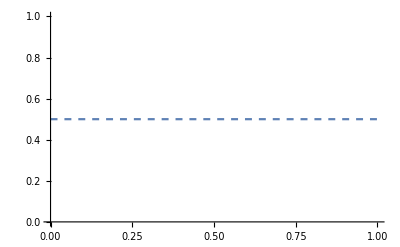

```mathematica
Plot[0.5, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->Dashed]
```

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

OptionValue::nodef: Unknown option PlotStyle for Graphics.

OptionValue::nodef: Unknown option PlotMarkers for Graphics.

OptionValue::nodef: Unknown option Joined for Graphics.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

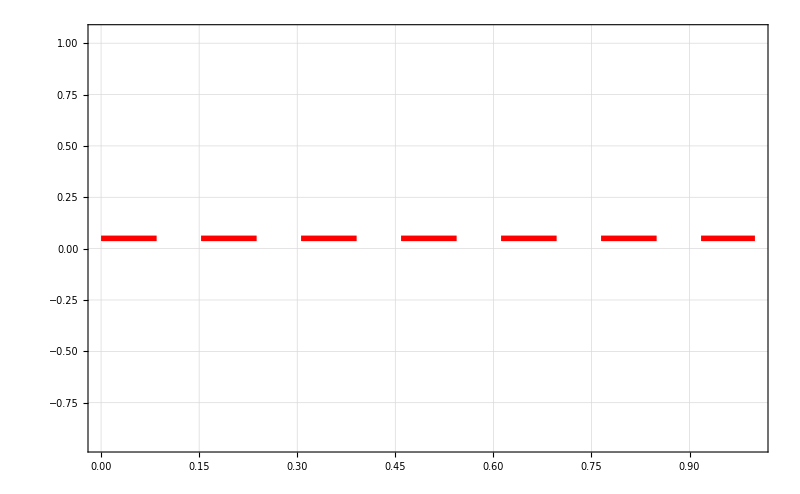

```mathematica
Show[ListPlot[ηsatislistnoNR, PlotStyle->Orange, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"Without NR step"},{{Center, 0.95}}]],ListPlot[ηsatislistNR, PlotStyle->Blue, Joined->True, PlotMarkers->{Automatic, 7}, PlotLegends->Placed[{"With NR step"}, {{Center, 0.95}}]], Plot[0.05, {x, 0, Length[ηsatislistnoNR]}, PlotStyle->{Thickness[0.005], Red, Dashing[{0.05, 0.04}]}, PlotLegends->Placed[{"Preset tolerance bound"}, {{Center, 0.95}}]], PlotRange->All, BaseStyle->{FontFamily->"Latin Modern Roman"}, Frame->True,FrameStyle->{Directive[Black,20],Directive[Black,20]}, GridLines->Automatic,PlotStyle->{Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]},PlotMarkers->{"+",20}, FrameLabel->{MaTeX[ToString["\\text{"<>"Discretisation step"<>"}"],Magnification->2],MaTeX[ToString["\\text{Error}~(e_1)"],Magnification->2]},Joined->True, ImageSize->800]
```

```mathematica
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
lsample = Inner[Rule, l, legvals[[1]], List]
```

{l1→1.44582+0. ⅈ,l2→1.56868+0. ⅈ,l3→1.57865+0. ⅈ,l4→1.33939+0. ⅈ,l5→1.15248+0. ⅈ,l6→1.28688+0. ⅈ}

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
ηconfig/.qrule/.htanrule//Variables
```

{l1,l2,l3,l4,l5,l6,p1,p2,p3,p4,p5,p6,s1,s2,s3,s4,s5,s6}

```mathematica
Denominator[Together[ηconfig/.qrule/.lsample/.htanrule]]
```

{(1.+p1^2) (1.+p2^2) (1.+s1^2) (1.+s2^2),(1.+p2^2) (1.+p3^2) (1.+s2^2) (1.+s3^2),(1.+p3^2) (1.+p4^2) (1.+s3^2) (1.+s4^2),(1.+p4^2) (1.+p5^2) (1.+s4^2) (1.+s5^2),(1.+p5^2) (1.+p6^2) (1.+s5^2) (1.+s6^2),(1.+p1^2) (1.+p6^2) (1.+s1^2) (1.+s6^2),(1.+p1^2) (1.+p3^2) (1.+s1^2) (1.+s3^2),(1.+p1^2) (1.+p4^2) (1.+s1^2) (1.+s4^2),(1.+p1^2) (1.+p5^2) (1.+s1^2) (1.+s5^2),(1.+p1^2) (1.+p2^2) (1.+p3^2) (1.+p4^2) (1.+s1^2) (1.+s2^2) (1.+s3^2) (1.+s4^2),(1.+p1^2) (1.+p3^2) (1.+p4^2) (1.+p5^2) (1.+s1^2) (1.+s3^2) (1.+s4^2) (1.+s5^2),(1.+p1^2) (1.+p4^2) (1.+p5^2) (1.+p6^2) (1.+s1^2) (1.+s4^2) (1.+s5^2) (1.+s6^2)}

```mathematica
ηlist = Numerator[Together[ηconfig/.qrule/.lsample/.htanrule]];
```

```mathematica
ηlist[[1]]//Simplify
```

-0.141788+1.70079 s1+8.93033 s1^2-1.84531 s2-18.1442 s1 s2-1.84531 s1^2 s2+8.93033 s2^2+1.70079 s1 s2^2-0.141788 s1^2 s2^2+p2 (-3.19617+3.19617 s2^2+s1^2 (-3.19617+3.19617 s2^2))+p2^2 (8.93033-1.84531 s2-0.141788 s2^2+s1 (1.70079-18.1442 s2+1.70079 s2^2)+s1^2 (-0.141788-1.84531 s2+8.93033 s2^2))+p1 (2.94585+2.94585 s2^2+s1^2 (-2.94585-2.94585 s2^2)+p2 (-18.1442+18.1442 s2^2+s1^2 (18.1442-18.1442 s2^2))+p2^2 (2.94585+2.94585 s2^2+s1^2 (-2.94585-2.94585 s2^2)))+p1^2 (8.93033-1.84531 s2-0.141788 s2^2+s1 (1.70079-18.1442 s2+1.70079 s2^2)+s1^2 (-0.141788-1.84531 s2+8.93033 s2^2)+p2^2 (-0.141788-1.84531 s2+8.93033 s2^2+s1^2 (8.93033-1.84531 s2-0.141788 s2^2)+s1 (1.70079-18.1442 s2+1.70079 s2^2))+p2 (-3.19617+3.19617 s2^2+s1^2 (-3.19617+3.19617 s2^2)))

```mathematica
initrule = Inner[Rule, qfull, initpose, List]
```

{x→0.2,y→0,z→1.28,c1→0.2,c2→0,c3→0,ϕ1→0.00305624-8.47269×10^-17 ⅈ,ϕ2→-0.0668855-8.94098×10^-17 ⅈ,ϕ3→0.456963-1.88509×10^-16 ⅈ,ϕ4→0.546956-7.59383×10^-17 ⅈ,ϕ5→-0.0946901-9.49786×10^-17 ⅈ,ϕ6→0.00349011-7.94231×10^-17 ⅈ,ψ1→0.336276-3.59163×10^-18 ⅈ,ψ2→0.286891-1.94522×10^-16 ⅈ,ψ3→-0.0210274-1.35667×10^-16 ⅈ,ψ4→0.0247844-1.74422×10^-16 ⅈ,ψ5→-0.395383-3.49377×10^-17 ⅈ,ψ6→-0.379795-1.31157×10^-16 ⅈ,l1→1.44582+0. ⅈ,l2→1.56868+0. ⅈ,l3→1.57865+0. ⅈ,l4→1.33939+0. ⅈ,l5→1.15248+0. ⅈ,l6→1.28688+0. ⅈ}

```mathematica
ηext/.lsample//Variables
```

{c1,c2,c3,x,y,z,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
(*FK of SRSPM is an unsolved problem*)
```

```mathematica
cJηext@@initpose//SingularValueList
```

{3.08517,2.80986,2.78322,2.52096,2.14729,2.06947,1.56372,1.50228,1.44022,1.382,1.32791,1.22903,1.17389,1.10881,1.0153,0.304377,0.244638,0.157325}

```mathematica
cJηext@@Join[{0.1, 0.1, 0.2, 0,0, 0}, iksol[{0.1, 0.1, 0.2, 0,0, 0}]]//SingularValueList
```

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

SingularValueList[CompiledFunction[…][{0.1,0.1,0.2,0,0,0},iksol[{0.1,0.1,0.2,0,0,0}]]]

```mathematica
bla = {0.1, 0.1, 0.2, 0, 0, 0};
initfrac = Rationalize[Join[bla, iksol[bla]], 0.000001]
```

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]]

```mathematica
fracrule = Inner[Rule, qfull, initfrac, List]
```

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]

```mathematica
ηlist = Numerator[Together[Rationalize[N[ηext/.fracrule[[-7;;]]/.htanrule], 0.000001]]];
```

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List].

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]⟦-7;;All⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{0.1,0.1,0.2,0.,0.,0.},iksol[{0.1,0.1,0.2,0.,0.,0.}]],List].

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{0.1,0.1,0.2,0.,0.,0.},iksol[{0.1,0.1,0.2,0.,0.,0.}]],List]⟦-7;;All⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and iksol at positions 1 and 2 are expected to be the same.

Inner::heads: Heads Join and List at positions 3 and 2 are expected to be the same.

Part::take: Cannot take positions -7 through -1 in Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List].

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
ηlist//Variables
```

{{452/617-(163 (2 c1 c2-2 c3))/(739 (1+c1^2+c2^2+c3^2))-(650 (1+c1^2-c2^2-c3^2))/(1211 (1+c1^2+c2^2+c3^2))+(2 l1 p1 (1-s1^2))/((1+p1^2) (1+s1^2))-x,437/642-(891 (c1 c2+c3))/(830 (1+c1^2+c2^2+c3^2))-(163 (1-c1^2+c2^2-c3^2))/(739 (1+c1^2+c2^2+c3^2))-(2 l1 s1)/(1+s1^2)-y,-(891 (-c2+c1 c3))/(830 (1+c1^2+c2^2+c3^2))-(326 (c1+c2 c3))/(739 (1+c1^2+c2^2+c3^2))+(l1 (1-p1^2) (1-s1^2))/((1+p1^2) (1+s1^2))-z,177/793-(356 (2 c1 c2-2 c3))/(619 (1+c1^2+c2^2+c3^2))+(55 (1+c1^2-c2^2-c3^2))/(711 (1+c1^2+c2^2+c3^2))+(2 l2 p2 (1-s2^2))/((1+p2^2) (1+s2^2))-x,966/991+(110 (c1 c2+c3))/(711 (1+c1^2+c2^2+c3^2))-(356 (1-c1^2+c2^2-c3^2))/(619 (1+c1^2+c2^2+c3^2))-(2 l2 s2)/(1+s2^2)-y,(110 (-c2+c1 c3))/(711 (1+c1^2+c2^2+c3^2))-(712 (c1+c2 c3))/(619 (1+c1^2+c2^2+c3^2))+(l2 (1-p2^2) (1-s2^2))/((1+p2^2) (1+s2^2))-z,-951/995-(401 (2 c1 c2-2 c3))/(1131 (1+c1^2+c2^2+c3^2))+(181 (1+c1^2-c2^2-c3^2))/(394 (1+c1^2+c2^2+c3^2))+(2 l3 p3 (1-s3^2))/((1+p3^2) (1+s3^2))-x,547/1860+(2206 (c1 c2+c3))/(2401 (1+c1^2+c2^2+c3^2))-(401 (1-c1^2+c2^2-c3^2))/(1131 (1+c1^2+c2^2+c3^2))-(2 l3 s3)/(1+s3^2)-y,(2206 (-c2+c1 c3))/(2401 (1+c1^2+c2^2+c3^2))-(841 (c1+c2 c3))/(1186 (1+c1^2+c2^2+c3^2))+(l3 (1-p3^2) (1-s3^2))/((1+p3^2) (1+s3^2))-z,-951/995+(401 (2 c1 c2-2 c3))/(1131 (1+c1^2+c2^2+c3^2))+(181 (1+c1^2-c2^2-c3^2))/(394 (1+c1^2+c2^2+c3^2))+(2 l4 p4 (1-s4^2))/((1+p4^2) (1+s4^2))-x,-547/1860+(2206 (c1 c2+c3))/(2401 (1+c1^2+c2^2+c3^2))+(401 (1-c1^2+c2^2-c3^2))/(1131 (1+c1^2+c2^2+c3^2))-(2 l4 s4)/(1+s4^2)-y,(2206 (-c2+c1 c3))/(2401 (1+c1^2+c2^2+c3^2))+(841 (c1+c2 c3))/(1186 (1+c1^2+c2^2+c3^2))+(l4 (1-p4^2) (1-s4^2))/((1+p4^2) (1+s4^2))-z,177/793+(356 (2 c1 c2-2 c3))/(619 (1+c1^2+c2^2+c3^2))+(55 (1+c1^2-c2^2-c3^2))/(711 (1+c1^2+c2^2+c3^2))+(2 l5 p5 (1-s5^2))/((1+p5^2) (1+s5^2))-x,-966/991+(110 (c1 c2+c3))/(711 (1+c1^2+c2^2+c3^2))+(356 (1-c1^2+c2^2-c3^2))/(619 (1+c1^2+c2^2+c3^2))-(2 l5 s5)/(1+s5^2)-y,(110 (-c2+c1 c3))/(711 (1+c1^2+c2^2+c3^2))+(712 (c1+c2 c3))/(619 (1+c1^2+c2^2+c3^2))+(l5 (1-p5^2) (1-s5^2))/((1+p5^2) (1+s5^2))-z,452/617+(163 (2 c1 c2-2 c3))/(739 (1+c1^2+c2^2+c3^2))-(650 (1+c1^2-c2^2-c3^2))/(1211 (1+c1^2+c2^2+c3^2))+(2 l6 p6 (1-s6^2))/((1+p6^2) (1+s6^2))-x,-437/642-(891 (c1 c2+c3))/(830 (1+c1^2+c2^2+c3^2))+(163 (1-c1^2+c2^2-c3^2))/(739 (1+c1^2+c2^2+c3^2))-(2 l6 s6)/(1+s6^2)-y,-(891 (-c2+c1 c3))/(830 (1+c1^2+c2^2+c3^2))+(326 (c1+c2 c3))/(739 (1+c1^2+c2^2+c3^2))+(l6 (1-p6^2) (1-s6^2))/((1+p6^2) (1+s6^2))-z}/.Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},Join[{1/10,1/10,1/5,0,0,0},iksol[{1/10,1/10,1/5,0,0,0}]],List]⟦-7;;All⟧}

```mathematica
fs = Table[Symbol["f"<>ToString[i]],{i, 18}];
```

```mathematica
Thread[fs == ηlist];
```

## Root tracking using the Nearest neighbour method:

```mathematica
(*Nearest neighbour method*)
```

```mathematica
(*This is will NR solver integrated with NN*)
```

To be done:
1. Find a method in C++ that can couple with the RT to find FK when RT fails

```mathematica
(*Lets come back to Nearest Neighbour later, start documenting the time and updating the C++ codes*)
```

```mathematica
replist=Union[{Power-> pow},{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]} ];
```

```mathematica
cformη = N[ηext]/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist//CForm;
```

```mathematica
(*Porting functions to CPP*)
```

```mathematica
Flatten[N[Jηext]/.Inner[Rule, Join[ϕ, ψ],  Join[p, s], List]/.replist]//CForm;
```

## Singularity manifold

```mathematica
g11 = ToExpression[Import["srspm_pos_eq1.txt"]]
```

0.00218325+0.00530428 x-0.0120075 x^2-0.00132539 y-0.0292269 x y-0.0124698 y^2-0.0375001 z+0.073172 x z+0.0108431 x^2 z+0.0412325 y z+0.0468517 x y z+0.0497715 y^2 z+0.0285304 z^2-0.10733 x z^2-0.217641 y z^2+0.205157 z^3

```mathematica
g11/.Inner[Rule,qfull,initposesC[[4]],List]
```

0.209491-0.162555 ⅈ

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp]
```

-Graphics3D-